```mathematica
SetDirectory[NotebookDirectory[]];
```

# Pre

```mathematica
nff[mf2_,q_,T_,μ_]:=If[(√(q^2+mf2)-μ)/T>60.,0.,1/(Exp[(√(q^2+mf2)-μ)/T]+1)];
nfa[mf2_,q_,T_,μ_]:=If[(√(q^2+mf2)+μ)/T>60.,0.,1/(Exp[(√(q^2+mf2)+μ)/T]+1)];
nfd1xf[mf2_,q_,T_,μ_]:=(nff[mf2,q,T,μ](nff[mf2,q,T,μ]-1.))/T;
nfd2xf[mf2_,q_,T_,μ_]:=(nff[mf2,q,T,μ](nff[mf2,q,T,μ]-1.)(2.*nff[mf2,q,T,μ]-1.))/T^2;
nfd1xa[mf2_,q_,T_,μ_]:=(nfa[mf2,q,T,μ](nfa[mf2,q,T,μ]-1.))/T;
nfd2xa[mf2_,q_,T_,μ_]:=(nfa[mf2,q,T,μ](nfa[mf2,q,T,μ]-1.)(2.*nfa[mf2,q,T,μ]-1.))/T^2;
mf2[h_,ρ_]:=(h^2 ρ)/2;
dmf2d1rho[h_,ρ_]:=h^2/2;
dmf2d2rho[h_,ρ_]:=0;
Nf=2;
Nc=3;
V[ρ_,h_,T_,μ_,λ_,ν_,c_]:=1/(4 π^2)NIntegrate[4*Nc*Nf*q^4*2/3*1/(2 √(q^2+mf2[h,ρ]))(0-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ]),{q,0,1000,5000}(*,AccuracyGoal->5,PrecisionGoal->5*),WorkingPrecision->10,Method->{"GlobalAdaptive","SymbolicProcessing"->0,Method->{"GaussBerntsenEspelidRule","Points"->10}},MaxRecursion->10]+(λ/2 ρ^2+ν ρ)-c √(2ρ);
Vvacuum[ρ_,h_,M_]:=(Nc Nf)/1*mf2[h,ρ]^2/(8 π^2)(-Log[(√mf2[h,ρ])/M]);
Vd1rhovacuum[ρ_,h_,λ_,ν_,M_]:=-(Nc Nf dmf2d1rho[h,ρ] mf2[h,ρ])/(16 π^2)-(Nc Nf dmf2d1rho[h,ρ] Log[(√mf2[h,ρ])/M] mf2[h,ρ])/(4 π^2)+(λ ρ+ν);
Vd2rhovacuum[ρ_,h_,λ_,ν_,M_]:=-1/8 Nc Nf ((2 dmf2d1rho[h,ρ]^2)/π^2+((-dmf2d1rho[h,ρ]^2/(2 mf2[h,ρ]^2)+dmf2d2rho[h,ρ]/(2 mf2[h,ρ])) mf2[h,ρ]^2)/π^2+(Log[(√mf2[h,ρ])/M] (2 dmf2d1rho[h,ρ]^2+2 dmf2d2rho[h,ρ] mf2[h,ρ]))/π^2)+λ;
h=6.5;
λ=41.1;
ν=-481.8^2;
c=1.7*10^-3*(10^3)^3;
μ=0.;
M1=500;
```

# Mean-field effective potential

## effective potential

NIntegrate::inumr: 在以 {{0,1000}} 为界的区域内，对于所有采样点，计算被积函数 (8 q^4 (-If[0.+√Plus[«2»]>60.,0.,1/(Exp[«1»]+1)]-If[0.+√Plus[«2»]>60.,0.,1/(Exp[«1»]+1)]))/(√(10.5625 a1^2+q^2)) 得到非数值.

FindMinimum::precw: 参数函数的精度 (-116066. a1^2+5.1375 a1^4-1.7×10^6 √(a1^2)-8.47803 a1^4 Log[0.0065 √(a1^2)]+NIntegrate[(4 Nc Nf q^4 2 (0-nff[mf2[«2»],q,1,0.]-nfa[mf2[«2»],q,1,0.]))/(3 (2 √(«1»))),{q,0,1000,5000},WorkingPrecision→10,Method→«1»,MaxRecursion→10]/(4 π^2)) 小于 WorkingPrecision (8.).

NIntegrate::precw: 参数函数的精度 ((8 q^4 (-If[√(Times[«2»]+Power[«2»])>60.,0.,1/(Exp[«1»]+1)]-If[√(Times[«2»]+Power[«2»])>60.,0.,1/(Exp[«1»]+1)]))/(√(10.5625 a1^2+q^2))) 小于 WorkingPrecision (10.).

N::preclg: 要求的精度 10. 大于 $MaxPrecision. 使用 8. 当前的 $MaxPrecision. $MaxPrecision = Infinity 指定应该允许任意精度.

NIntegrate::inumr: 在以 {{0,1000}} 为界的区域内，对于所有采样点，计算被积函数 -(16 q^4 If[√(10.5625 a1^2+q^2)>60.,0,1/(1+ⅇ^(√Plus[«2»]))])/(√(10.5625 a1^2+q^2)) 得到非数值.

NIntegrate::precw: 参数函数的精度 ((8 q^4 (-If[√(Times[«2»]+Power[«2»])>60.,0.,1/(Exp[«1»]+1)]-If[√(Times[«2»]+Power[«2»])>60.,0.,1/(Exp[«1»]+1)]))/(√(10.5625 a1^2+q^2))) 小于 WorkingPrecision (10.).

N::preclg: 要求的精度 10. 大于 $MaxPrecision. 使用 8. 当前的 $MaxPrecision. $MaxPrecision = Infinity 指定应该允许任意精度.

NIntegrate::inumr: 在以 {{0,1000}} 为界的区域内，对于所有采样点，计算被积函数 -(16 q^4 If[√(10.5625 a1^2+q^2)>60.,0,1/(1+ⅇ^(√Plus[«2»]))])/(√(10.5625 a1^2+q^2)) 得到非数值.

General::stop: 在本次计算中，NIntegrate::inumr 的进一步输出将被抑制.

NIntegrate::precw: 参数函数的精度 ((8 q^4 (-If[√(Times[«2»]+Power[«2»])>60.,0.,1/(Exp[«1»]+1)]-If[√(Times[«2»]+Power[«2»])>60.,0.,1/(Exp[«1»]+1)]))/(√(10.5625 a1^2+q^2))) 小于 WorkingPrecision (10.).

General::stop: 在本次计算中，NIntegrate::precw 的进一步输出将被抑制.

N::preclg: 要求的精度 10. 大于 $MaxPrecision. 使用 8. 当前的 $MaxPrecision. $MaxPrecision = Infinity 指定应该允许任意精度.

General::stop: 在本次计算中，N::preclg 的进一步输出将被抑制.

NIntegrate::izero: 在所有积分子区域上，积分和误差估计都是 0. 请尝试增加 MinRecursion 选项的值. 如果积分值可能是 0，为 AccuracyGoal 选项指定一个有限制.

General::stop: 在本次计算中，NIntegrate::izero 的进一步输出将被抑制.

92.339896

135.684

479.934

300.105

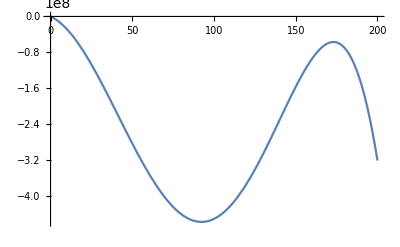

```mathematica
a=FindMinimum[{V[a1^2/2,h,1,0.,λ,ν,c]+Vvacuum[a1^2/2,h,M1],0<a1<195},{a1,90},WorkingPrecision->8][[2]][[1]][[2]]
(*a*√Zps[a^2/2,h,1.,0.,M1]*)
√(Vd1rhovacuum[a^2/2,h,λ,ν,M1]/(Zps[a^2/2,h,1.,0.,M1]*0.+1.))
√((Vd1rhovacuum[a^2/2,h,λ,ν,M1]+2*a^2/2*Vd2rhovacuum[a^2/2,h,λ,ν,M1])/(Zps[a^2/2,h,1.,0.,M1]*0.+1.))
√mf2[h,a^2/2]
Plot[{(*V[a^2/2,h,1,0,λ,ν,c],Vvacuum[a^2/2,h,1000],*)V[a^2/2,h,1,0,λ,ν,c]+Vvacuum[a^2/2,h,M1]},{a,0,200},PlotRange->All]
(*Zps[a^2/2,h,1.,0.,M1]*)
```

```mathematica
(*fpi=Flatten[Table[{FindMinimum[{V[a^2/2,h,i,μ,λ,ν,c]+Vvacuum[a^2/2,h,M1],0<a<95},{a,50},AccuracyGoal->10,PrecisionGoal->10][[2]][[1]][[2]]},{i,1,300}]];*)
```

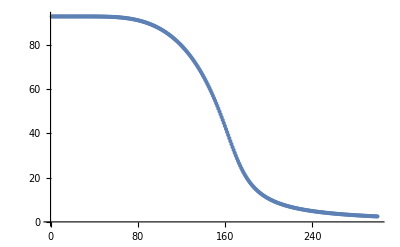

```mathematica
ListPlot[fpi,PlotRange->All]
```

## 1st derivative

## 2nd derivative

# Mean-field wave function renormalization

## threshold functions

```mathematica
F2[q_,ρ_,h_,T_,μ_]:=1/(4.*(q^2+mf2[h,ρ])^(3/2))(√(q^2+mf2[h,ρ])nfd1xa[mf2[h,ρ],q,T,μ]+√(q^2+mf2[h,ρ])nfd1xf[mf2[h,ρ],q,T,μ]+0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ])*q^3;
F3[q_,ρ_,h_,T_,μ_]:=q^5/(16.*(q^2+mf2[h,ρ])^(5/2))(-((q^2+mf2[h,ρ])(nfd2xf[mf2[h,ρ],q,T,μ]+nfd2xa[mf2[h,ρ],q,T,μ]))+3(√(q^2+mf2[h,ρ])*nfd1xf[mf2[h,ρ],q,T,μ]+√(q^2+mf2[h,ρ])*nfd1xa[mf2[h,ρ],q,T,μ]+0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ]));
```

## thermal equation

```mathematica
Zpsthr[ρ_,h_,T_,μ_]:=-2 h^2 Nc NIntegrate[1/(q 2 π^2)(-F2[q,ρ,h,T,μ]+2/3 F3[q,ρ,h,T,μ]),{q,0.,500.,5000.}(*,{x,-1,1},{y,0,2π}*),AccuracyGoal->15,PrecisionGoal->15,MaxRecursion->20];
```

## Regularized vacuum

```mathematica
Zpsvac[ρ_,h_,M_]:=-(Nc h^2)/(8 π^2)Log[(√mf2[h,ρ])/M];
```

## Zps(0)

## Yukawa input data

```mathematica
hin[x_]:=a+b x+c1 x^2+d x^3+e x^4+f x^5+g x^6+h1 x^7+i x^8+j x^9/.{a->0.9957909545322429,b->0.001714257771479005,c1->-0.0001783382102583089,d->7.65973368936231*^-6,e->-1.5961805729197664*^-7,f->1.877596391835684*^-9,g->-1.3189343683401787*^-11,h1->5.429783784945215*^-14,i->-1.2017089289406018*^-16,j->1.1009372159449776*^-19};
```

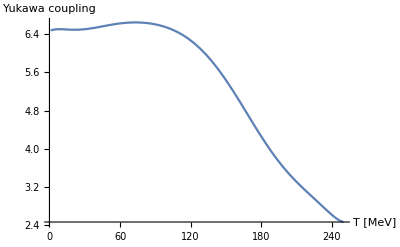

```mathematica
hplot=Plot[hin[x]*6.5,{x,1,250},AxesLabel->{"T [MeV]","Yukawa coupling"}]
```

```mathematica
Export["h.pdf",hplot]
```

h.pdf

```mathematica
hindata=Flatten[Table[hin[x]*6.5,{x,1,250}]];
```

## Z_π data

```mathematica
Zps[ρ_,h_,T_,μ_,M_]:=Zpsthr[ρ,h,T,μ]+Zpsvac[ρ,h,M]+1.;
```

```mathematica
Zall=Flatten[Table[Zps[fpimub0[[i]]^2/2,h(*indata[[i]]*),N[i],0.,500.],{i,1,300}]];
(*Zvall=Flatten[Table[Zpsvac[fpi[[i]]^2/2,h,500.],{i,1,300}]];*)
(*Zvint=Flatten[Table[Zpsthr[fpi[[i]]^2/2,h,1.,μ],{i,1,300}]];*)
```

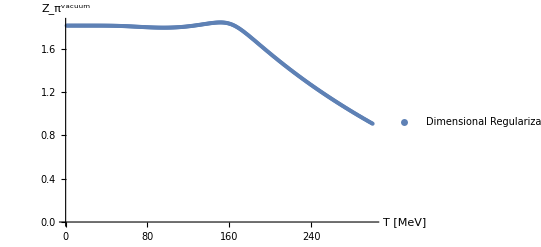

```mathematica
plotvac=ListPlot[{Zall},PlotRange->{{0,300},All},AxesLabel->{"T [MeV]","Z_π^vacuum"},PlotLegends->{"Dimensional Regularization  M=500 MeV","UV cut-off   Λ=700 MeV"}]
```

```mathematica
Export["./vac.pdf",plotvac]
```

./vac.pdf

# Mean-field two-point function

## threshold functions

```mathematica
F1[q_,ρ_,h_,T_,μ_]:=q/(2 √(q^2+mf2[h,ρ]))(0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ]);
F1F1m[q_,p0_,ps_,x_,ρ_,h_,T_,μ_]:=(*If[Abs[√(q^2+mf2[h,ρ])-√((q^2+ps^2-2q ps x)+mf2[h,ρ])]/(√(q^2+mf2[h,ρ]))>10^-5,*)q^3/(4 √(q^2+mf2[h,ρ])√((q^2+ps^2-2q ps x)+mf2[h,ρ]))((-0.+nff[mf2[h,ρ],√(q^2+ps^2-2q ps x),T,μ]+nfa[mf2[h,ρ],q,T,μ])/(ⅈ p0-√(q^2+mf2[h,ρ])-√((q^2+ps^2-2q ps x)+mf2[h,ρ]))+(nfa[mf2[h,ρ],√(q^2+ps^2-2q ps x),T,μ]-nfa[mf2[h,ρ],q,T,μ])/(ⅈ p0-√(q^2+mf2[h,ρ])+√((q^2+ps^2-2q ps x)+mf2[h,ρ]))+(nff[mf2[h,ρ],q,T,μ]-nff[mf2[h,ρ],√(q^2+ps^2-2q ps x),T,μ])/(ⅈ p0+√(q^2+mf2[h,ρ])-√((q^2+ps^2-2q ps x)+mf2[h,ρ]))+(0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],√(q^2+ps^2-2q ps x),T,μ])/(ⅈ p0+√(q^2+mf2[h,ρ])+√((q^2+ps^2-2q ps x)+mf2[h,ρ])))(*,q^3/(4(√(q^2+mf2[h,ρ]))^2)((-0.+nff[mf2[h,ρ],q,T,μ]+nfa[mf2[h,ρ],q,T,μ])/(ⅈ p0-√(q^2+mf2[h,ρ])-√(q^2+mf2[h,ρ]))+nfd1xa[mf2[h,ρ],q,T,μ]+nfd1xf[mf2[h,ρ],q,T,μ]+(0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ])/(ⅈ p0+√(q^2+mf2[h,ρ])+√(q^2+mf2[h,ρ])))]*);
```

## thermal equation

```mathematica
gamma2thr[p0_,ps_,ρ_,h_,T_,μ_]:=-(h^2 Nc)/(2π)^3 NIntegrate[q^2/q(2F1[q,ρ,h,T,μ]-(p0^2+ps^2)/q^2 F1F1m[q,p0,ps,x,ρ,h,T,μ]),{q,0.,500.,5000.},{x,-1,1},{y,0,2π},
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->10];
```

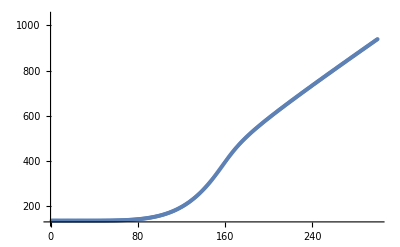

```mathematica
ListPlot[√(gammathrmu0+(λ fpimu0^2/2+ν)+gammavacdata),PlotRange->{{0,300},{130,1040}}]
```

## Regularized vacuum

```mathematica
gammavac[p0_,ps_,ρ_,h_,Mmass_,MZ_]:=-(Nc h^2)/(8 π^2)((2Log[(√mf2[h,ρ])/Mmass])mf2[h,ρ]+(p0^2+ps^2)/2 NIntegrate[Log[(-(p0^2+ps^2)(x-1)^2-x(p0^2+ps^2)+(p0^2+ps^2)+mf2[h,ρ])/MZ^2],{x,0,1}])(*+(p0^2+ps^2)/2EulerGamma-(p0^2+ps^2)/2 Log[4π]*)-(Nc h^2 mf2[h,ρ])/(16 π^2);
```

## full two-point function

```mathematica
gamma2[p0_,ps_,ρ_,h_,T_,μ_,Mmass_,MZ_]:=gamma2thr[p0,ps,ρ,h,T,μ]+gammavac[p0,ps,ρ,h,Mmass,MZ];
```

```mathematica
gammadata=Flatten[ParallelTable[gamma2[-ⅈ(i*10+ⅈ 0.5),j*50.,fpimu0[[100]]^2/2,h,100.,0.,700.,300.]+(-ⅈ(i*10))^2+(j*50.)^2+(λ fpimu0[[100]]^2/2+ν),{i,1,100},{j,1,20}]];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.201156}. NIntegrate obtained -1.30382-1.8825 ⅈ and 0.000010207 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.810531}. NIntegrate obtained -1.24398-1.93891 ⅈ and 0.000012561 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.839828}. NIntegrate obtained -1.02257-2.12388 ⅈ and 0.000029137 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.210922}. NIntegrate obtained -1.36569-1.8208 ⅈ and 6.24022×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.183578}. NIntegrate obtained -1.18604-1.99072 ⅈ and 0.0000227119 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.845688}. NIntegrate obtained -0.971222-2.16219 ⅈ and 0.0000781018 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.13475}. NIntegrate obtained -0.779382-2.2926 ⅈ and 7.84561×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.150375}. NIntegrate obtained -0.9213-2.19799 ⅈ and 0.0000497248 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.871078}. NIntegrate obtained -0.734476-2.3205 ⅈ and 0.000114811 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.874984}. NIntegrate obtained -0.690675-2.34685 ⅈ and 0.000128749 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

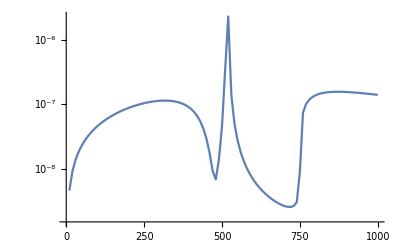

```mathematica
ListLinePlot[Transpose[{Flatten[Table[i*10,{i,1,100}]],-1/π Im[gammadata]/(Re[gammadata]^2+Im[gammadata]^2)}],PlotRange->All,ScalingFunctions->"Log"]
```

# Plot data

## fpi

```mathematica
fpimu0=Flatten[Table[{FindMinimum[{V[a^2/2,h,i,0.,λ,ν,c]+Vvacuum[a^2/2,h,M1],0<a<95},{a,50},AccuracyGoal->10,PrecisionGoal->10][[2]][[1]][[2]]},{i,1,300}]];
```

NIntegrate::inumr: 在以 {{0,1000}} 为界的区域内，对于所有采样点，计算被积函数 (8 q^4 (-If[0.+√Plus[«2»]>60.,0.,1/(Exp[«1»]+1)]-If[0.+√Plus[«2»]>60.,0.,1/(Exp[«1»]+1)]))/(√(19.847 a^2+q^2)) 得到非数值.

NIntegrate::izero: 在所有积分子区域上，积分和误差估计都是 0. 请尝试增加 MinRecursion 选项的值. 如果积分值可能是 0，为 AccuracyGoal 选项指定一个有限制.

NIntegrate::inumr: 在以 {{0,1000}} 为界的区域内，对于所有采样点，计算被积函数 (8 q^4 (-If[0.+√Plus[«2»]>60.,0.,1/(Exp[«1»]+1)]-If[0.+√Plus[«2»]>60.,0.,1/(Exp[«1»]+1)]))/(√(19.847 a^2+q^2)) 得到非数值.

General::stop: 在本次计算中，NIntegrate::inumr 的进一步输出将被抑制.

NIntegrate::izero: 在所有积分子区域上，积分和误差估计都是 0. 请尝试增加 MinRecursion 选项的值. 如果积分值可能是 0，为 AccuracyGoal 选项指定一个有限制.

General::stop: 在本次计算中，NIntegrate::izero 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {q} = {89.8406993} 处的 q 中进行 10 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -3.760409357×10^-18 和 2.656541367×10^-21.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {q} = {89.8406993} 处的 q 中进行 10 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -3.761653782×10^-18 和 2.657386825×10^-21.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

NIntegrate::ncvb: 在接近 {q} = {89.8406993} 处的 q 中进行 10 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -3.759165343×10^-18 和 2.655696177×10^-21.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: 在本次计算中，FindMinimum::acceptlev 的进一步输出将被抑制.

```mathematica
fpimu100=Flatten[Table[{FindMinimum[{V[a^2/2,h,i,100.,λ,ν,c]+Vvacuum[a^2/2,h,M1],0<a<95},{a,50},AccuracyGoal->10,PrecisionGoal->10][[2]][[1]][[2]]},{i,1,300}]];
```

```mathematica
fpimu200=Flatten[Table[{FindMinimum[{V[a^2/2,h,i,200.,λ,ν,c]+Vvacuum[a^2/2,h,M1],0<a<95},{a,50},AccuracyGoal->10,PrecisionGoal->10][[2]][[1]][[2]]},{i,1,300}]];
```

```mathematica
fpimu300=Flatten[Table[{FindMinimum[{V[a^2/2,h,i,300.,λ,ν,c]+Vvacuum[a^2/2,h,M1],0<a<95},{a,50},AccuracyGoal->10,PrecisionGoal->10][[2]][[1]][[2]]},{i,1,300}]];
```

NIntegrate::inumr: 在以 {{0,1000}} 为界的区域内，对于所有采样点，计算被积函数 (8 q^4 (-If[-300.+√Plus[«2»]>60.,0.,1/(Exp[«1»]+1)]-If[300.+√Plus[«2»]>60.,0.,1/(Exp[«1»]+1)]))/(√(19.847 a^2+q^2)) 得到非数值.

General::stop: 在本次计算中，NIntegrate::inumr 的进一步输出将被抑制.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: 在本次计算中，FindMinimum::acceptlev 的进一步输出将被抑制.

```mathematica
fpimu250=Flatten[Table[{FindMinimum[{V[a^2/2,h,i,250.,λ,ν,c]+Vvacuum[a^2/2,h,M1],0<a<95},{a,50},AccuracyGoal->10,PrecisionGoal->10][[2]][[1]][[2]]},{i,1,300}]];
```

```mathematica
fpimu260=Flatten[Table[{FindMinimum[{V[a^2/2,h,i,260.,λ,ν,c]+Vvacuum[a^2/2,h,M1],0<a<95},{a,50},AccuracyGoal->10,PrecisionGoal->10][[2]][[1]][[2]]},{i,1,300}]];
```

```mathematica
fpimu280=Flatten[Table[{FindMinimum[{V[a^2/2,h,i,280.,λ,ν,c]+Vvacuum[a^2/2,h,M1],0<a<95},{a,50},AccuracyGoal->10,PrecisionGoal->10][[2]][[1]][[2]]},{i,1,300}]];
```

```mathematica
fpimu290=Flatten[Table[{FindMinimum[{V[a^2/2,h,i,290.,λ,ν,c]+Vvacuum[a^2/2,h,M1],0<a<95},{a,50},AccuracyGoal->10,PrecisionGoal->10][[2]][[1]][[2]]},{i,1,300}]];
```

```mathematica
fpimu295=Flatten[Table[{FindMinimum[{V[a^2/2,h,i,295.,λ,ν,c]+Vvacuum[a^2/2,h,M1],0<a<95},{a,50},AccuracyGoal->10,PrecisionGoal->10][[2]][[1]][[2]]},{i,1,300}]];
```

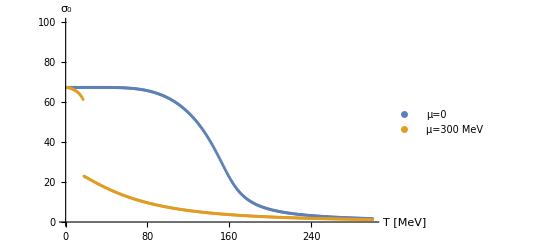

```mathematica
fpiplot=ListPlot[{fpimu0,(*fpimu200,fpimu250,fpimu295,*)fpimu300},AxesLabel->{"T [MeV]","σ_0"},PlotRange->{All,{0,100}},PlotLegends->{"μ=0",(*"μ=200 MeV","μ=250 MeV","μ=295 MeV",*)"μ=300 MeV"}]
```

```mathematica
Export["fpi.pdf",fpiplot]
```

fpi.pdf

## Z_π(p=0)

### M=400

```mathematica
Zmu0M350=Flatten[Table[Zps[fpimu0[[i]]^2/2,h,N[i],0.,M1],{i,1,300}]];
```

```mathematica
Zmu300M350=Flatten[Table[Zps[fpimu300[[i]]^2/2,h,N[i],300.,M1],{i,1,300}]];
```

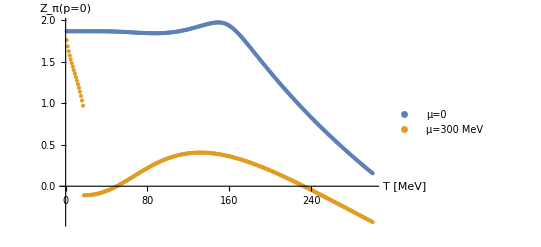

```mathematica
ZplotM300=ListPlot[{Zmu0M350,Zmu300M350},AxesLabel->{"T [MeV]","Z_π(p=0)"},PlotRange->{All,All},PlotLegends->{"μ=0","μ=300 MeV"}]
```

```mathematica
Export["ZM300.pdf",ZplotM300]
```

ZM300.pdf